```mathematica
wignerP[β_,αI_,αR_]:=Abs[Exp[-Abs[αR+I αI]^2/2 - Abs[β]^2/2+(αR-I αI)β]]^2
```

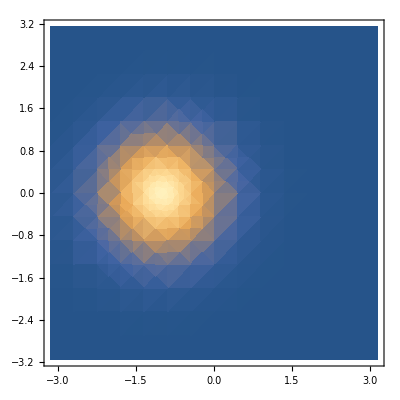

```mathematica
DensityPlot[wignerP[Exp[-I π ],y,x],{x,-π,π},{y,-π,π},
PlotRange-> {{-π ,π },{- π ,π },{0,1}}]
```

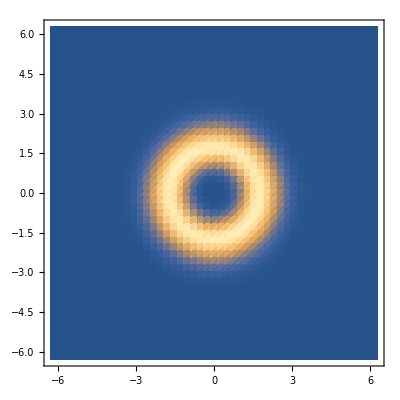

```mathematica
DensityPlot[Abs[Exp[-Abs[x+I y]^2/2](x+ I y)^3/(3!)^(1/2)]^2,{x,-π 2,π 2},{y,-π 2,π 2},
PlotRange-> {{-π 2 ,π 2 },{- π 2 ,π 2},{0,1}},
PlotPoints-> 50]
```

```mathematica
Manipulate[
DensityPlot[Abs[Cos[θ/2] Exp[-Abs[x+I y]^2/2]+Exp[I ϕ]Sin[θ/2]Exp[-Abs[x+I y]^2/2](x+ I y)^3/(3!)^(1/2)]^2,{x,-π 2,π 2},{y,-π 2,π 2},
PlotRange-> {{-π 2 ,π 2 },{- π 2 ,π 2},{0,1}},
PlotPoints-> 50]
,{θ,0,π},{ϕ,0,2 π}]
```

```mathematica
CohPsi[α_,n_]:=Exp[-Abs[α]^2/2](α^n/√(n!) )
```

```mathematica
Manipulate[
Plot[Abs[CohPsi[n,x]],{x,0,10},
PlotRange-> {{0,10},{0,1}}],
{n,0.001,10}
]
```

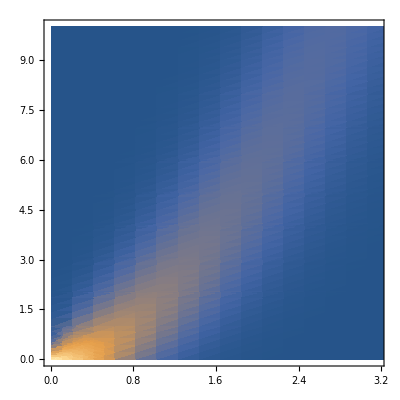

```mathematica
DensityPlot[Abs[CohPsi[n,x] CohPsi[n+1,x]],{n,0.01,10},{x,0.01,10},
PlotRange-> {{0,√10},{0 ,10},{0,1}},
PlotPoints-> 50]
```

```mathematica
PsiHON[n_,x_]:=1/(√(2^n n!))(1/π)^(1/4)Exp[- x^2/2]HermiteH[n,x];
(*PsiHON[n_,x_]:=PsiHO[n,x]/√NIntegrate[Abs[PsiHO[n,y]]^2,{y,-1000,1000}]*)
```

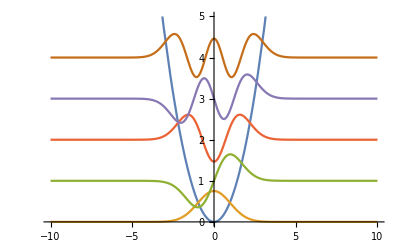

```mathematica
Plot[{x^2/2,
PsiHON[0,x],
PsiHON[1,x]+1,
PsiHON[2,x]+2,
PsiHON[3,x]+3,
PsiHON[4,x]+4},{x,-10,10},
PlotRange-> {{-10,10},{0,5}}]
```

```mathematica
TestPsiN[x_,S_]:=1/(√(2π S^2))Exp[-(x)^2/(2 S^2)] ;
(*TestPsiN[x_,S_]:=TestPsi[x,S]/√NIntegrate[Abs[TestPsi[y,S]]^2,{y,-1000,1000}]*)
TestPsiND[x_,d_,S_]:=1/(√(2π S^2))Exp[-(x-d)^2/(2 S^2)] ;
(*TestPsiN[x_,d_,S_]:=TestPsi[x,d,S]/√NIntegrate[Abs[TestPsi[y,d,S]]^2,{y,-1000,1000}]*)
```

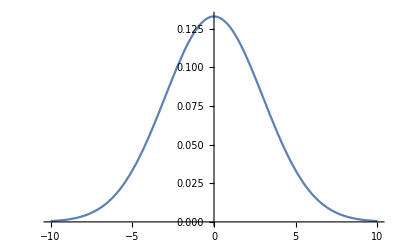

```mathematica
Plot[TestPsiN[x,3],{x,-10,10}]
```

```mathematica
OverlapInt[n_,S_]:=NIntegrate[TestPsiN[x,S]* PsiHON[n,x],{x,-Infinity,Infinity}]
OverlapIntD[n_,d_,S_]:=NIntegrate[TestPsiN[x,d,S]* PsiHON[n,x],{x,-Infinity,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.79352×10^-8}. NIntegrate obtained -3.68629×10^-17 and 8.39733×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.747488}. NIntegrate obtained 8.0231×10^-18 and 3.92598×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.30639}. NIntegrate obtained -2.34188×10^-17 and 3.08471×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

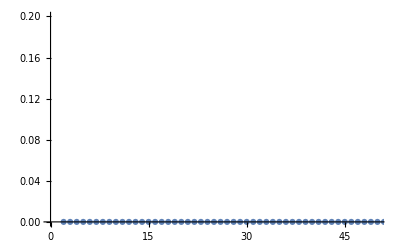
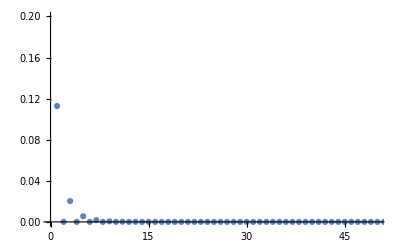
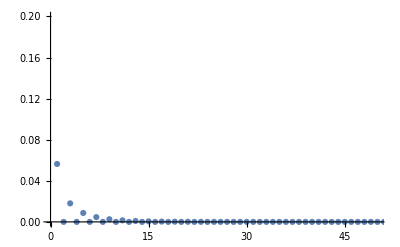
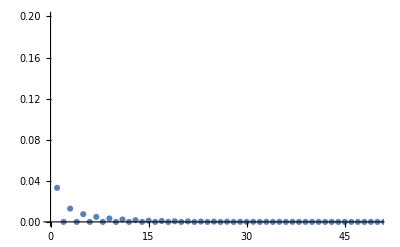
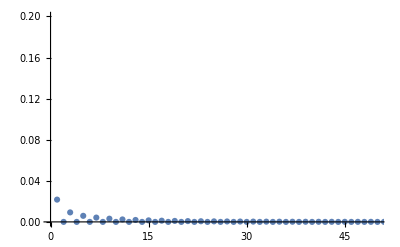
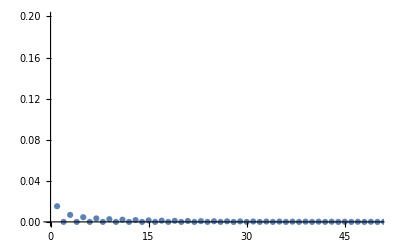
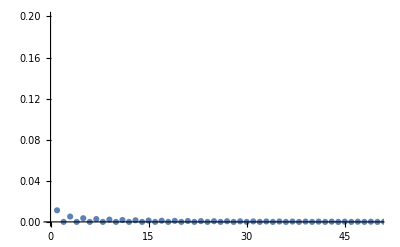
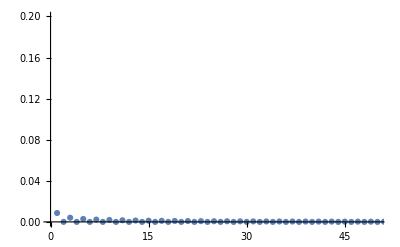

```mathematica
Table[
ListPlot[(Table[{ii,OverlapInt[ii,S]},{ii,0,50}]⟦;;,2⟧)^2,
PlotRange-> {{0,50},{0,0.2}}],
{S,1,10}
]
```

```mathematica
Table[
ListPlot[(Table[{ii,OverlapIntD[ii,D,3]},{ii,0,75}]⟦;;,2⟧)^2,
PlotRange-> {{0,75},{0,0.2}}],
{D,1,10}
]
```

NIntegrate::inumr: The integrand (ⅇ^(-x^2/2) TestPsiN[x,1,3])/π^(1/4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (√2 ⅇ^(-x^2/2) x TestPsiN[x,1,3])/π^(1/4) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (ⅇ^(-x^2/2) (-2+4 x^2) TestPsiN[x,1,3])/(2 √2 π^(1/4)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {7.78142}. NIntegrate obtained 3.74554 and 0.00001202 for the integral and error estimates.

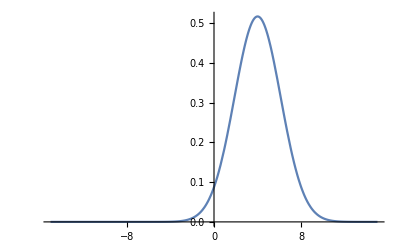

```mathematica
Plot[TestPsiN[x,4,3],{x,-15,15}]
```

```mathematica
PsiT[t_,x_,d_,S_]:=Total[Table[TestPsiND[x,d,S]* PsiHON[n,x] Exp[I (n+1/2)π 2t],{n,0,75}]]
Manipulate[
Plot[Abs[PsiT[t,x,4,3]]^2,{x,-15,15}]
,{t,0,10}]
```

```mathematica
Coh[x_,w_]:=1/(√(2 π 5^2))Exp[-x^2/5] 1/(2 w)4Integrate[1+Cos[2 π x + W ],{W,-w,w}];
SCoh[x_,w_]:=1/(√(2 π 5^2))Exp[-x^2/5](1+Cos[2 π x] Sin[w]/w)
```

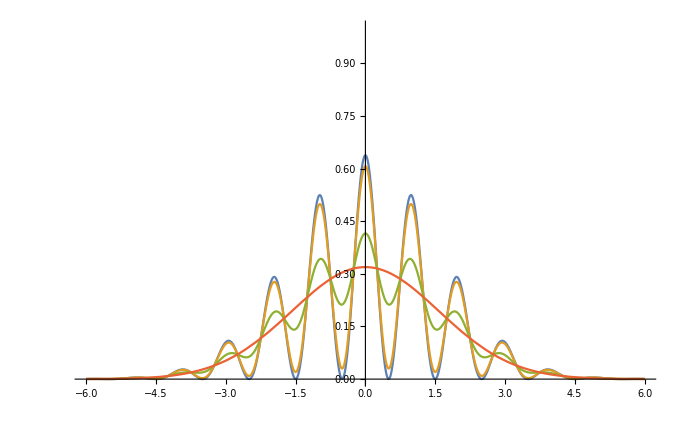

```mathematica
Plot[{Coh[x,0.1],Coh[x,π/4],Coh[x,3 π/4],Coh[x, π]},{x,-6,6},
PlotRange-> {{-6,6},{0,1}}]
```

```mathematica
Manipulate[
Plot[SCoh[x,w],{x,-10,10},
PlotRange-> {{-5,5},{0,0.2}}],
{w,0.01,10 π 0.99}
]
```

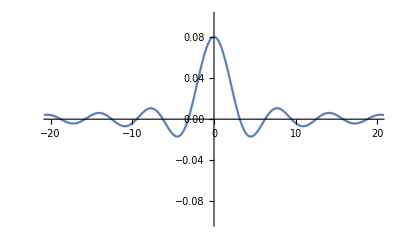

```mathematica
Plot[SCoh[0,w]-SCoh[0,100],{w,-100,100},
PlotRange-> {{-20,20},{-0.1,0.1}}]
```

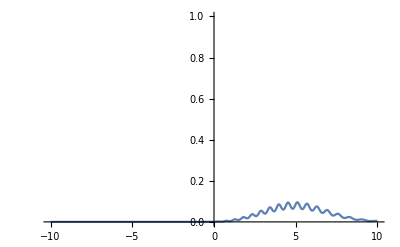
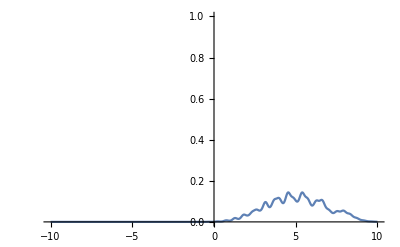
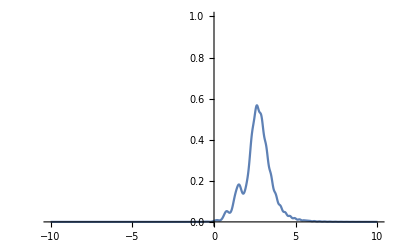
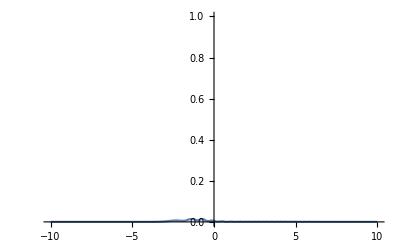
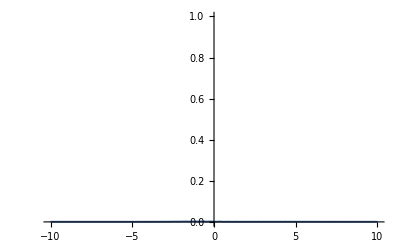
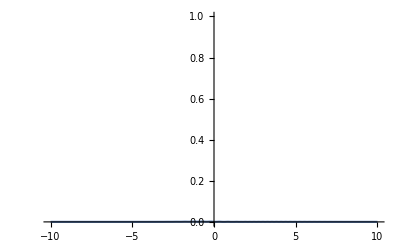
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Plot[Abs[Total[Table[TestPsiND[x,4,3]* PsiHON[n,x] Exp[-I (n+1/2)π 2t],{n,0,70}]]/.t-> tt]^2,{x,-10,10},
PlotRange-> {{-10,10},{0,1}}],
{tt,0,1,0.1}]
```

```mathematica
CohPsi[α_,x_,N_]:=Exp[-Abs[α]^2/2]Total[Table[α^n/√(n!)PsiHON[n,x],{n,0,N}]]
```

Table::itraw: Raw object 75 cannot be used as an iterator.

General::stop: Further output of Table::itraw will be suppressed during this calculation.

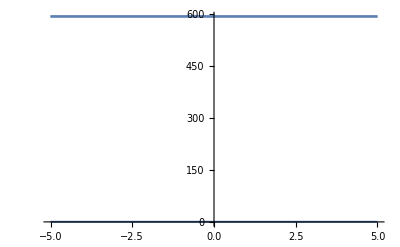

```mathematica
Plot[Abs[CohPsi[3/2,x,75]]^2,{x,-5,5}]
```